# Quantica

## Calculator of quantum systems with mathematica

20 December, 2013

## Baker-Campbell-Hausdorff展開

Baker-Campbell-Hausdorff展開の公式は互いに非可換なx,yにたいして

e^x e^y=e^z
z= x+ y + ∑_(j=2)^∞ z_j

と展開される．ここでz_jはxとyの交換間関係が入れ子になった級数として求まる．
各j番目のz_jをmathematicaを用いて交換関係を展開した形式で求める．
なおj>2でなければならない．

```mathematica
Get["Quantica`"];
Quantica`BCH`Translated2[2]
```

xy/2-yx/2

```mathematica
Quantica`BCH`Translated2[3]
```

xxy/12-xyx/6+xyy/12+yxx/12-yxy/6+yyx/12

同様に3項のBCH展開

e^x e^y e^w=e^z
z= x+ y + w + ∑_(j=2)^∞ z_j

は

```mathematica
Quantica`BCH`Translated3[2]
```

-wx/2-wy/2+xw/2+xy/2+yw/2-yx/2

としてとともめる事が可能である．
さらに対称性がある場合

e^x e^y e^x=e^z
z= 2x+ y + ∑_(j=2)^∞ z_j

は

```mathematica
Quantica`BCH`Translated3S[2]
Quantica`BCH`Translated3S[3]
Quantica`BCH`Translated3S[4]
```

0

-xxy/6+xyx/3+xyy/6-yxx/6-yxy/3+yyx/6

0

となる．対称な場合z_j の偶数次はゼロとなる

### 量子写像のBCH展開近似

量子写像にBCH公式を適用し

exp[-i/ℏT(p)τ]exp[-i/ℏV(p)τ]≃exp[-i/ℏ H_eff^(m)τ]

H_eff^(m)(q,p)= T(p) + V(q) + ∑_(j=2)^m H_j(q,p)

Sumをm次までで打ち切る事で近似的に求まる時間に依存しないハミルトニアンを求める．

```mathematica
Get["Quantica`"];
Quantica`MP`dps=20;
T[x_]:=x*x/2
V[x_]:=Cos[2*Pi*x]/(4*Pi*Pi)
dim=70;
domain={{0,1},{-1,1}};
QuanticaSetting[dim,domain,tau->6/10];
SetSystem[T,V];
matT=Quantica`FourierBase`MatrixT[];
matV=Quantica`FourierBase`MatrixV[];
Ham=Quantica`FourierBase`Hamiltonian[];
A=-I*matT*Tau/Hbar;
B=-I*matV*Tau/Hbar;
evals = {};
```

```mathematica
For[i=0,i<5,i++,
res = Quantica`BCH`BCH2[i,A,B,Verbose->True];
mat= Hbar*I*res/Tau;
evals=Append[evals,Eigen[mat,Vector->False]];
];
```

{2 word BCH series:,2}

{2 word BCH series:,2}

{2 word BCH series:,3}

{2 word BCH series:,2}

{2 word BCH series:,3}

{2 word BCH series:,4}

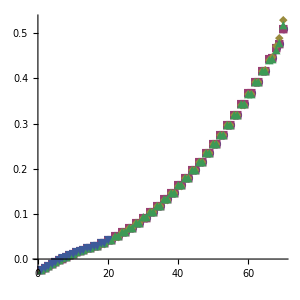

```mathematica
ListPlot[Table[  Re[evals[[i]]  ],{i,1,Length[evals]} ],
PlotMarkers->{Automatic,Small},ImageSize->{300,300},AspectRatio->Full]
```

3項の場合は

```mathematica
For[i=1,i<6,i+=2,
res = Quantica`BCH`BCH3[i,B/2,A,B/2,Verbose->True];
mat= Hbar*I*res/Tau;
evals=Append[evals,Eigen[mat,Vector->False]];
];
```

{2 word Symmetric BCH series:,2}

{2 word Symmetric BCH series:,3}

{2 word Symmetric BCH series:,2}

{2 word Symmetric BCH series:,3}

{2 word Symmetric BCH series:,4}

{2 word Symmetric BCH series:,5}

```mathematica
ListPlot[Table[  Re[evals[[i]]  ],{i,1,Length[evals]} ],
PlotMarkers->{Automatic,Small},ImageSize->{300,300},AspectRatio->Full]
```

-Graphics-

とすればよい．